# Scattering rate

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
solndir=FileNameJoin[{NotebookDirectory[],"\\solns\\"}];
Do[
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],dir}]];,
{dir,{constsdir,imagedir,solndir}}
]
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 15],ImageSize->Medium];
```

## single atom in free space

### scattering vs frequency

```mathematica
scatter=γ(Int/(2IntS))/(1+(4(2π δ)^2)/γ^2+Int/IntS);
γ =ΓD2;
P = 3.5*^-6;
Int = P/(π*6*^-6*8*^-6);
"Saturation intensity [mW/cm^2]"
IntS =3.05*10^-3*10^4;(*[W/m^2] (ℏ γ (2π (νD2*10^12-2.563*^9+267*^6))^3)/(12π c^2)*);
IntS*10^3*10^-4
```

Saturation intensity [mW/cm^2]

3.05

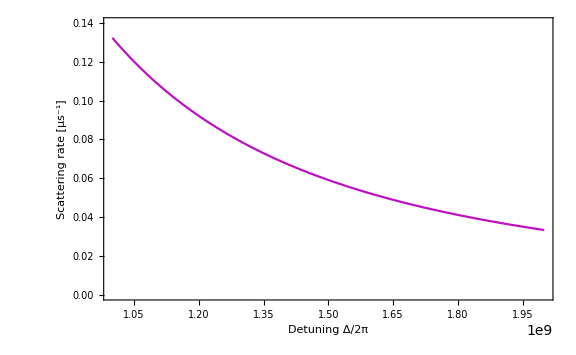

```mathematica
Plot[scatter*1*^-6,{δ,1*^9,2*^9},LabelStyle->Directive[Black,Medium],Axes->Off,Frame->{True,True,False,False},FrameLabel->{"Detuning Δ/2π","Scattering rate [μs^-1]"},PlotStyle->RGBColor[RandomReal[],RandomReal[],RandomReal[]],ImageSize->Large,PlotRange->{0,.14}]
```

So on average, < 0.04 photons are scattered per 1 μs time interval if our light is 2 GHz detuned. For a π pulse to a Rydberg W state with a mean of N atoms is  t_π=π/Ω_N=π/(√N Ω).

```mathematica
"photons scattered during W state pi pulse"
π/(√10 5*^5)*10^6*0.04
```

photons scattered during W state pi pulse

0.0794767

### vs wavelength with constant dipole trap depth

We can have the scattering rate at each wavelength point be for a fixed trapping potential (e.g. if the light is red detuned) by calculating the intensity from the polarizability and desired trap depth. This way, the scattering rate plot is actually useful for selecting a dipole trap wavelength.

```mathematica
IntT[Ttrap_,α0_]:=(2 kB Ttrap)/α0 c ϵ0;
scatterλ=γ(IntT[Ttrap,α0]/(2IntS*10))/(1+(4(2π)^2)/γ^2(c/λ0^2(λ0-λ))^2+IntT[Ttrap,α0]/(IntS*10));
scatterD2 = scatterλ/.{IntS->IsatD2,γ-> ΓD2,λ0->λD2 };
scatterD1 = scatterλ/.{IntS->IsatD1,γ-> ΓD1,λ0->λD1 };
```

```mathematica
α0data = Transpose@Import[FileNameJoin[{solndir,"five_s_onehalf_dynamic_alpha0_0.8um_to_1.064um_40steps.csv"}]];
labels=α0data[[1]];
α0data =Transpose@(α0data[[2;;]]);
λpts = α0data[[1]];
αSIpts=α0data[[3]];
```

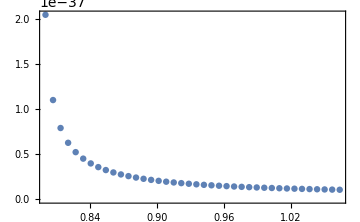

```mathematica
ListPlot[Transpose@{λpts*10^6, αSIpts},PlotRange->All]
```

```mathematica
scatterDlineConstTTrap [T_]:=Table[(scatterD1+scatterD2)/.{α0->u[[1]],λ-> u[[2]],Ttrap-> T},{u,Transpose@{αSIpts,λpts}}];
```

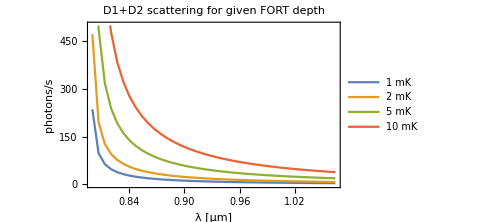

```mathematica
TList = {1,2,5,10};
plt=ListPlot[Evaluate[Table[Transpose@{λpts*1*^6,scatterDlineConstTTrap[mk*1*^-3]},{mk,TList}]],FrameLabel->{"λ [μm]", "photons/s"},PlotRange->{0,500},PlotLegends->Map[StringForm["`` mK",#]&,TList],PlotLabel->"D1+D2 scattering for given FORT depth",Joined->True]
```

```mathematica
(*Export["dline_scattering_vs_wavelength_1_2_5_10mK.png",plt]*)
```

dline_scattering_vs_wavelength_1_2_5_10mK.png

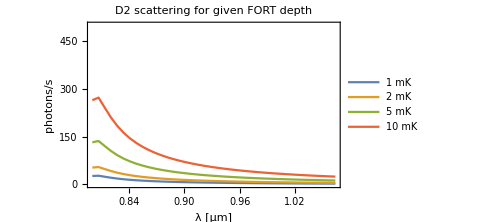

```mathematica
scatterD1lineConstTTrap [T_]:=Table[scatterD1/.{α0->u[[1]],λ-> u[[2]],Ttrap-> T},{u,Transpose@{αSIpts,λpts}}]
scatterD2lineConstTTrap [T_]:=Table[scatterD2/.{α0->u[[1]],λ-> u[[2]],Ttrap-> T},{u,Transpose@{αSIpts,λpts}}];
TList = {1,2,5,10};
plt=ListPlot[Evaluate[Table[Transpose@{λpts*1*^6,scatterD2lineConstTTrap[mk*1*^-3]},{mk,TList}]],FrameLabel->{"λ [μm]", "photons/s"},PlotRange->{0,500},PlotLegends->Map[StringForm["`` mK",#]&,TList],PlotLabel->"D2 scattering for given FORT depth",Joined->True]
```

```mathematica
Export["d2line_scattering_vs_wavelength_1_2_5_10mK.png",plt]
```

d2line_scattering_vs_wavelength_1_2_5_10mK.png

Just to check that the intensity scales as we expect, we can plot the power required for a given wavelength and trap depth, given a beam with a 1 μm waist.

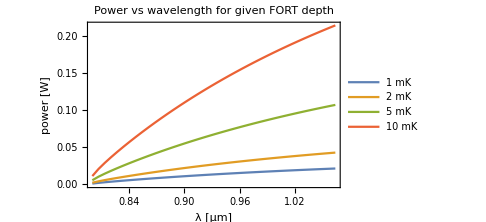

```mathematica
intensityTable =Table[ (2kB T)/α0 c ϵ0,{α0,αSIpts}];
plt=ListPlot[Evaluate[Table[Transpose@{λpts*1*^6,intensityTable*π(1*^-6)^2/.T-> mk*1*^-3},{mk,TList}]],FrameLabel->{"λ [μm]", "power [W]"},PlotLegends->Map[StringForm["`` mK",#]&,TList],PlotLabel->"Power vs wavelength for given FORT depth",Joined->True,LabelStyle->Directive[Black, 14]]
```

```mathematica
(*Export["trap_1um_waist_power_vs_wavelength_1_2_5_10mK.png",plt]*)
```

trap_1um_waist_power_vs_wavelength_1_2_5_10mK.png

sanity check. power in W for a dipole trap at 1064 w/ 3 um waist:

```mathematica
(2kB 1*^-3)/αSIpts[[-1]] c ϵ0 *π*(3*^-6)^2
```

0.193341